```mathematica
MinGen[X_] := If[FreeQ[X,Around],Min[X],Min[#["Value"]& /@ X]];
MaxGen[X_] := If[FreeQ[X,Around],Max[X],Max[#["Value"]& /@ X]]
```

```mathematica
MinVal[L_, n_]:= MinGen[Transpose[L][[n]]];
```

```mathematica
MaxVal[L_, n_]:= MaxGen[Transpose[L][[n]]];
```

```mathematica
MinGen[{Around[1,0.1],Around[3,0.2]}]
```

1.

```mathematica
MinGen[{1,0.1,3,0.2}]
```

0.1

```mathematica
MyDnSample[L_, n_] := L[[#]]& /@Range[1,Length[L],n];
```

```mathematica
DataWithErrors[data_,n_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[Sort[data,#1[[n]]<#2[[n]]&],bins];
```

```mathematica
DataWithErrors[data_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[data,bins];
```

```mathematica
DataWithWeights[data_, bins_]:={Mean[#],Sqrt[bins]/StandardDeviation[#]}& /@ Partition[data,bins];
```

```mathematica
{dd,ww} =Transpose[DataWithWeights[Table[N[{x, Sin[Pi x]}],{x,-1,1,1/1000}],100]]
```

{{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386},{-0.4505,-0.983876},{-0.3505,-0.888056},{-0.2505,-0.705308},{-0.1505,-0.453519},{-0.0505,-0.157337},{0.0495,0.154247},{0.1495,0.450732},{0.2495,0.703096},{0.3495,0.886636},{0.4495,0.983386},{0.5495,0.983876},{0.6495,0.888056},{0.7495,0.705308},{0.8495,0.453519},{0.9495,0.157337}},{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386},{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386}}}

```mathematica
dd[[;;5]]
```

{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386}}

```mathematica
ww[[;;5]]
```

{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834}}

```mathematica
Around[#[[1]],#[[2]]]& /@Transpose[{{m,m,m},{s,s,s}}]
```

{ms,ms,ms}

```mathematica
ttt=Transpose[{Table[RandomReal[],4],Table[RandomReal[],4],Table[RandomReal[],4]}]
```

{{0.188293,0.338314,0.0879526},{0.613869,0.980297,0.820077},{0.816228,0.225902,0.996844},{0.893788,0.722363,0.666985}}

```mathematica
Mean[#]& /@Partition[ttt,2]
```

{{0.401081,0.659305,0.454015},{0.855008,0.474133,0.831915}}

```mathematica
ttt[[;;3]]
```

{{0.188293,0.338314,0.0879526},{0.613869,0.980297,0.820077},{0.816228,0.225902,0.996844}}

```mathematica
Transpose[{{1,2},{a,b}, {x,y}}]
```

{{1,a,x},{2,b,y}}

```mathematica
test = Transpose[{ttt}];
```

```mathematica
Dimensions[ttt]
```

{4,3}

```mathematica
test =DataWithErrors[ArrayReshape[Sort[Table[RandomReal[],256]],{64,4}],4]
```

{{0.0430.013,0.0490.013,0.0520.014,0.0570.016},{0.1270.016,0.1340.017,0.1400.015,0.1450.014},{0.2000.010,0.2070.012,0.2120.012,0.2150.011},{0.2540.005,0.2560.005,0.2570.005,0.2580.006},{0.3140.014,0.3210.011,0.3240.011,0.3300.013},{0.3950.013,0.3990.014,0.4000.014,0.4080.013},{0.4510.008,0.4560.007,0.4590.008,0.4610.009},{0.4920.005,0.4950.005,0.4960.005,0.4960.005},{0.5420.013,0.5460.014,0.5490.014,0.5550.013},{0.6020.007,0.6050.005,0.6080.005,0.6100.004},{0.6480.008,0.6520.007,0.6540.007,0.6550.007},{0.6920.009,0.6940.009,0.6970.008,0.6980.009},{0.7500.011,0.7520.011,0.7580.009,0.7610.009},{0.8220.012,0.8240.012,0.8280.010,0.8360.010},{0.8790.011,0.8860.012,0.8880.012,0.8930.012},{0.9370.008,0.9430.012,0.9490.014,0.9530.016}}

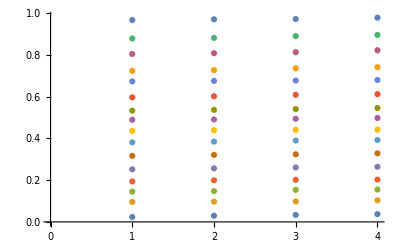

```mathematica
ListPlot[test]
```

```mathematica
ShowFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{"data"}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, Thick},
PlotLegends->{N[model[Xlabel],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
ShowLogFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{Ylabel}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, PointSize[0.5]},
PlotLegends->{N[FullSimplify[Exp[model[Log[x]]]],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
```

```mathematica
ShowLogFitModelBin[data_,bins_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
ShowLogFitModel[DataWithErrors[data,1,bins], model,Xlabel,Ylabel, title, dcol, mcol];
```

```mathematica
ClearAll[NumericalVector];
```

```mathematica
NumericalVector[{}] = False;
```

```mathematica
NumericVector[X_] := And @@(NumericQ  /@ X);
```

```mathematica
NumericVector[{1,2,3}]
```

True

```mathematica
edectab={{-4.605170185988091,8.411754927159429},{-4.586749505244138,8.411754884354794},{-4.5683288245001865,8.411754840755801},{-4.549908143756234,8.411754796347722},{-4.531487463012282,8.411754751115557},{-4.5130667822683295,8.411754705044029},{-4.494646101524377,8.411754658117571},{-4.476225420780424,8.411754610320342},{-4.457804740036472,8.411754561636192},{-4.43938405929252,8.411754512048685},{-4.420963378548567,8.411754461541072},{-4.402542697804615,8.4117544100963},{-4.384122017060663,8.411754357696994},{-4.36570133631671,8.411754304325465},{-4.347280655572758,8.411754249963689},{-4.328859974828806,8.411754194593316},{-4.310439294084854,8.411754138195649},{-4.292018613340901,8.411754080751649},{-4.273597932596949,8.411754022241928},{-4.255177251852996,8.41175396264673},{-4.236756571109044,8.411753901945943},{-4.218335890365092,8.411753840119076},{-4.199915209621139,8.411753777145265},{-4.181494528877187,8.411753713003254},{-4.1630738481332346,8.411753647671397},{-4.144653167389282,8.411753581127648},{-4.12623248664533,8.41175351334955},{-4.1078118059013775,8.411753444314238},{-4.089391125157425,8.411753373998414},{-4.070970444413473,8.411753302378356},{-4.0525497636695205,8.411753229429902},{-4.034129082925568,8.41175315512844},{-4.015708402181615,8.411753079448909},{-3.9972877214376634,8.411753002365778},{-3.9788670406937108,8.411752923853049},{-3.9604463599497586,8.411752843884242},{-3.9420256792058064,8.411752762432384},{-3.9236049984618537,8.411752679470007},{-3.9051843177179015,8.411752594969133},{-3.886763636973949,8.41175250890127},{-3.8683429562299967,8.411752421237393},{-3.8499222754860445,8.41175233194795},{-3.831501594742092,8.411752241002835},{-3.8130809139981396,8.41175214837139},{-3.794660233254187,8.411752054022385},{-3.776239552510235,8.41175195792402},{-3.7578188717662826,8.411751860043902},{-3.73939819102233,8.411751760349043},{-3.7209775102783778,8.411751658805843},{-3.702556829534425,8.41175155538008},{-3.684136148790473,8.411751450036906},{-3.6657154680465203,8.411751342740823},{-3.6472947873025685,8.411751233455679},{-3.628874106558616,8.411751122144654},{-3.6104534258146637,8.41175100877025},{-3.592032745070711,8.411750893294274},{-3.573612064326759,8.41175077567783},{-3.555191383582806,8.411750655881299},{-3.536770702838854,8.411750533864337},{-3.5183500220949018,8.411750409585851},{-3.4999293413509496,8.41175028300399},{-3.481508660606997,8.411750154076131},{-3.4630879798630447,8.411750022758861},{-3.444667299119092,8.411749889007972},{-3.42624661837514,8.411749752778434},{-3.4078259376311877,8.411749614024387},{-3.389405256887235,8.41174947269913},{-3.370984576143283,8.41174932875509},{-3.35256389539933,8.411749182143826},{-3.334143214655378,8.411749032815997},{-3.3157225339114254,8.411748880721355},{-3.297301853167473,8.411748725808723},{-3.278881172423521,8.411748568025981},{-3.2604604916795688,8.411748407320047},{-3.242039810935616,8.41174824363686},{-3.223619130191664,8.411748076921361},{-3.2051984494477113,8.411747907117483},{-3.186777768703759,8.41174773416812},{-3.1683570879598064,8.41174755801511},{-3.149936407215854,8.41174737859922},{-3.1315157264719016,8.411747195860123},{-3.11309504572795,8.411747009736384},{-3.094674364983997,8.411746820165433},{-3.076253684240045,8.411746627083549},{-3.0578330034960928,8.411746430425827},{-3.03941232275214,8.411746230126182},{-3.020991642008188,8.411746026117296},{-3.0025709612642357,8.411745818330619},{-2.9841502805202835,8.411745606696334},{-2.965729599776331,8.411745391143343},{-2.9473089190323782,8.41174517159923},{-2.928888238288426,8.411744947990254},{-2.9104675575444734,8.411744720241309},{-2.892046876800521,8.411744488275907},{-2.873626196056569,8.411744252016153},{-2.855205515312617,8.411744011382718},{-2.836784834568664,8.411743766294808},{-2.8183641538247115,8.411743516670148},{-2.7999434730807593,8.411743262424945},{-2.781522792336807,8.411743003473863},{-2.763102111592855,8.411742739729997},{-2.744681430848902,8.41174247110484},{-2.7262607501049496,8.41174219750826},{-2.707840069360998,8.411741918848463},{-2.6894193886170457,8.411741635031968},{-2.670998707873093,8.411741345963572},{-2.652578027129141,8.411741051546322},{-2.634157346385188,8.41174075168148},{-2.615736665641236,8.411740446268498},{-2.5973159848972833,8.411740135204969},{-2.578895304153331,8.411739818386613},{-2.5604746234093785,8.411739495707224},{-2.5420539426654263,8.41173916705865},{-2.523633261921474,8.411738832330746},{-2.5052125811775214,8.411738491411347},{-2.4867919004335692,8.411738144186222},{-2.468371219689617,8.411737790539043},{-2.4499505389456644,8.411737430351346},{-2.431529858201712,8.411737063502486},{-2.41310917745776,8.411736689869606},{-2.3946884967138073,8.41173630932759},{-2.376267815969855,8.411735921749024},{-2.357847135225903,8.411735527004154},{-2.3394264544819503,8.411735124960844},{-2.3210057737379977,8.411734715484531},{-2.3025850929940455,8.411734298438184},{-2.2841644122500933,8.411733873682252},{-2.265743731506141,8.411733441074626},{-2.2473230507621884,8.41173300047059},{-2.2289023700182358,8.411732551722773},{-2.2104816892742836,8.411732094681097},{-2.1920610085303314,8.411731629192733},{-2.1736403277863787,8.411731155102046},{-2.1552196470424265,8.411730672250549},{-2.136798966298474,8.411730180476848},{-2.1183782855545217,8.411729679616586},{-2.0999576048105695,8.411729169502399},{-2.081536924066617,8.411728649963848},{-2.0631162433226646,8.411728120827375},{-2.044695562578712,8.411727581916242},{-2.02627488183476,8.411727033050475},{-2.007854201090808,8.4117264740468},{-1.9894335203468554,8.411725904718578},{-1.9710128396029032,8.41172532487576},{-1.952592158858951,8.411724734324814},{-1.9341714781149986,8.41172413286866},{-1.915750797371046,8.411723520306614},{-1.8973301166270937,8.411722896434316},{-1.878909435883141,8.411722261043666},{-1.8604887551391889,8.411721613922756},{-1.8420680743952367,8.411720954855799},{-1.8236473936512843,8.411720283623062},{-1.8052267129073318,8.411719600000787},{-1.7868060321633792,8.411718903761132},{-1.768385351419427,8.41171819467208},{-1.7499646706754746,8.411717472497372},{-1.7315439899315221,8.411716736996427},{-1.71312330918757,8.411715987924275},{-1.6947026284436177,8.411715225031463},{-1.676281947699665,8.411714448063982},{-1.6578612669557125,8.411713656763185},{-1.6394405862117605,8.411712850865696},{-1.621019905467808,8.411712030103335},{-1.6025992247238559,8.411711194203017},{-1.5841785439799032,8.411710342886675},{-1.565757863235951,8.411709475871163},{-1.5473371824919986,8.411708592868168},{-1.528916501748046,8.411707693584114},{-1.5104958210040937,8.41170677772007},{-1.4920751402601413,8.411705844971651},{-1.473654459516189,8.41170489502892},{-1.4552337787722363,8.411703927576285},{-1.4368130980282847,8.411702942292406},{-1.4183924172843323,8.411701938850072},{-1.3999717365403799,8.411700916916114},{-1.3815510557964277,8.411699876151296},{-1.363130375052475,8.411698816210194},{-1.3447096943085228,8.4116977367411},{-1.3262890135645706,8.411696637385894},{-1.3078683328206184,8.41169551777994},{-1.2894476520766658,8.411694377551958},{-1.2710269713327134,8.411693216323915},{-1.2526062905887607,8.41169203371089},{-1.234185609844808,8.411690829320964},{-1.215764929100856,8.411689602755077},{-1.1973442483569035,8.411688353606923},{-1.1789235676129515,8.411687081462807},{-1.1605028868689988,8.411685785901508},{-1.1420822061250466,8.411684466494155},{-1.1236615253810942,8.411683122804076},{-1.1052408446371418,8.411681754386674},{-1.0868201638931894,8.411680360789271},{-1.0683994831492372,8.411678941550964},{-1.0499788024052845,8.411677496202483},{-1.031558121661332,8.41167602426604},{-1.0131374409173801,8.411674525255176},{-0.9947167601734275,8.411672998674602},{-0.976296079429475,8.411671444020044},{-0.957875398685523,8.411669860778085},{-0.9394547179415704,8.411668248425991},{-0.921034037197618,8.41166660643155},{-0.9026133564536655,8.411664934252904},{-0.884192675709713,8.411663231338382},{-0.8657719949657606,8.41166149712632},{-0.847351314221809,8.411659731044876},{-0.8289306334778566,8.411657932511861},{-0.8105099527339044,8.411656100934543},{-0.7920892719899515,8.411654235709465},{-0.7736685912459994,8.411652336222245},{-0.7552479105020471,8.411650401847396},{-0.7368272297580948,8.411648431948114},{-0.7184065490141424,8.411646425876084},{-0.6999858682701899,8.41164438297127},{-0.6815651875262373,8.411642302561704},{-0.663144506782285,8.411640183963273},{-0.6447238260383327,8.411638026479507},{-0.6263031452943802,8.411635829401371},{-0.6078824645504279,8.411633592007036},{-0.5894617838064755,8.411631313561637},{-0.5710411030625233,8.41162899331706},{-0.552620422318571,8.411626630511694},{-0.5341997415746187,8.411624224370197},{-0.515779060830666,8.41162177410325},{-0.4973583800867137,8.41161927890731},{-0.4789376993427614,8.411616737964358},{-0.46051701859880895,8.41161415044166},{-0.4420963378548566,8.411611515491478},{-0.42367565711090416,8.41160883225081},{-0.40525497636695185,8.41160609984112},{-0.3868342956229997,8.411603317368076},{-0.3684136148790471,8.411600483921267},{-0.3499929341350948,8.411597598573904},{-0.3315722533911424,8.41159466038254},{-0.31315157264718985,8.411591668386784},{-0.2947308919032375,8.411588621608987},{-0.2763102111592856,8.411585519053952},{-0.2578895304153332,8.411582359708614},{-0.23946884967138102,8.411579142541733},{-0.22104816892742854,8.411575866503565},{-0.2026274881834758,8.411572530525552},{-0.18420680743952383,8.411569133519977},{-0.16578612669557144,8.411565674379636},{-0.14736544595161913,8.411562151977487},{-0.12894476520766635,8.411558565166304},{-0.11052408446371438,8.411554912778334},{-0.09210340371976193,8.411551193624911},{-0.07368272297580956,8.411547406496108},{-0.05526204223185683,8.411543550160367},{-0.036841361487904546,8.411539623364126},{-0.018420680743952294,8.411535624831425},{0.,8.411531553263499},{0.018420680743952523,8.411527407338404},{0.036841361487905025,8.411523185710596},{0.0552620422318571,8.411518887010528},{0.07368272297580973,8.411514509844222},{0.0921034037197619,8.411510052792858},{0.11052408446371421,8.411505514412319},{0.12894476520766676,8.411500893232777},{0.14736544595161946,8.411496187758242},{0.16578612669557136,8.411491396466102},{0.18420680743952425,8.411486517806626},{0.2026274881834763,8.411481550202526},{0.22104816892742876,8.41147649204847},{0.239468849671381,8.41147134171061},{0.2578895304153335,8.411466097526073},{0.27631021115928556,8.411460757802459},{0.29473089190323815,8.41145532081733},{0.3131515726471905,8.411449784817696},{0.3315722533911431,8.411444148019475},{0.3499929341350951,8.411438408606957},{0.3684136148790477,8.411432564732275},{0.3868342956230004,8.411426614514834},{0.4052549763669526,8.411420556040751},{0.4236756571109051,8.411414387362285},{0.4420963378548575,8.41140810649725},{0.4605170185988096,8.41140171142842},{0.47893769934276204,8.411395200102929},{0.49735838008671474,8.411388570431662},{0.5157790608306667,8.411381820288607},{0.5341997415746192,8.41137494751023},{0.5526204223185716,8.411367949894874},{0.5710411030625239,8.411360825202092},{0.5894617838064753,8.411353571151976},{0.6078824645504276,8.411346185424474},{0.62630314529438,8.411338665658702},{0.6447238260383327,8.41133100945225},{0.663144506782285,8.411323214360475},{0.6815651875262373,8.41131527789579},{0.6999858682701895,8.411307197526916},{0.7184065490141421,8.411298970678134},{0.7368272297580942,8.411290594728536},{0.7552479105020468,8.411282067011298},{0.7736685912459994,8.411273384812903},{0.7920892719899516,8.411264545372292},{0.8105099527339038,8.411255545880048},{0.8289306334778563,8.411246383477602},{0.8473513142218085,8.411237055256407},{0.8657719949657611,8.411227558257094},{0.8841926757097135,8.411217889468606},{0.9026133564536658,8.411208045827335},{0.9210340371976181,8.411198024216235},{0.9394547179415706,8.411187821463916},{0.957875398685523,8.41117743434374},{0.9762960794294749,8.411166859572871},{0.9947167601734275,8.411156093811329},{1.0131374409173801,8.411145133661062},{1.0315581216613325,8.411133975664999},{1.049978802405285,8.411122616306033},{1.0683994831492372,8.411111052006005},{1.0868201638931896,8.411099279124684},{1.1052408446371418,8.411087293958747},{1.1236615253810944,8.411075092740715},{1.142082206125047,8.41106267163789},{1.160502886868999,8.411050026751257},{1.1789235676129517,8.411037154114423},{1.1973442483569037,8.41102404969248},{1.2157649291008563,8.411010709380832},{1.2341856098448087,8.410997129004077},{1.2526062905887612,8.410983304314817},{1.2710269713327134,8.410969230992487},{1.2894476520766658,8.410954904642137},{1.3078683328206184,8.410940320793216},{1.3262890135645706,8.410925474898317},{1.344709694308523,8.410910362331924},{1.363130375052475,8.410894978389125},{1.3815510557964277,8.410879318284303},{1.3999717365403799,8.41086337714982},{1.4183924172843323,8.410847150034678},{1.4368130980282847,8.410830631903154},{1.4552337787722374,8.41081381763341},{1.4736544595161893,8.410796702016102},{1.492075140260142,8.41077927975295},{1.5104958210040942,8.410761545455303},{1.5289165017480466,8.410743493642661},{1.547337182491999,8.41072511874116},{1.5657578632359515,8.410706415082092},{1.5841785439799039,8.410687376900395},{1.6025992247238563,8.41066799833308},{1.6210199054678087,8.410648273417657},{1.6394405862117607,8.41062819609053},{1.6578612669557136,8.410607760185359},{1.6762819476996655,8.410586959431415},{1.6947026284436182,8.410565787451901},{1.7131233091875708,8.410544237762265},{1.731543989931522,8.410522303768463},{1.7499646706754743,8.410499978765225},{1.768385351419427,8.410477255934277},{1.7868060321633794,8.410454128342549},{1.8052267129073312,8.410430588940356},{1.823647393651284,8.410406630559553},{1.8420680743952362,8.410382245911643},{1.8604887551391884,8.410357427585922},{1.8789094358831409,8.410332168047509},{1.8973301166270933,8.41030645963535},{1.915750797371046,8.410280294560277},{1.9341714781149983,8.410253664902992},{1.9525921588589505,8.41022656261206},{1.971012839602903,8.410198979501832},{1.9894335203468554,8.410170907250283},{2.0078542010908076,8.410142337396909},{2.0262748818347602,8.410113261340625},{2.0446955625787124,8.410083670337558},{2.063116243322665,8.410053555498886},{2.0815369240666173,8.410022907788633},{2.0999576048105695,8.409991718021164},{2.118378285554522,8.409959976858742},{2.1367989662984743,8.40992767480939},{2.1552196470424265,8.409894802224475},{2.173640327786379,8.409861349296463},{2.1920610085303314,8.409827306056695},{2.2104816892742836,8.40979266237279},{2.228902370018236,8.409757407946335},{2.247323050762189,8.409721532310286},{2.265743731506141,8.409685024825993},{2.2841644122500937,8.409647874680669},{2.302585092994046,8.409610070884993},{2.3210057737379985,8.409571602270223},{2.3394264544819503,8.40953245748538},{2.357847135225903,8.409492624994703},{2.3762678159698556,8.40945209307504},{2.394688496713808,8.409410849812982},{2.41310917745776,8.409368883101852},{2.431529858201712,8.40932618063897},{2.449950538945665,8.409282729922722},{2.468371219689617,8.409238518249628},{2.4867919004335697,8.40919353271145},{2.505212581177522,8.409147760192061},{2.523633261921474,8.409101187364438},{2.5420539426654267,8.409053800687555},{2.5604746234093794,8.409005586403213},{2.5788953041533316,8.40895653053292},{2.5973159848972838,8.408906618874722},{2.6157366656412364,8.408855836999901},{2.6341573463851886,8.40880417024972},{2.652578027129141,8.40875160373223},{2.6709987078730935,8.408698122318857},{2.6894193886170457,8.408643710640812},{2.7078400693609983,8.408588353085639},{2.7262607501049505,8.40853203379381},{2.744681430848903,8.40847473665514},{2.7631021115928553,8.408416445305106},{2.7815227923368075,8.408357143121568},{2.7999434730807597,8.408296813221318},{2.8183641538247124,8.408235438456183},{2.836784834568665,8.408173001409315},{2.8552055153126172,8.408109484391504},{2.8736261960565694,8.408044869437228},{2.892046876800521,8.407979138300757},{2.9104675575444734,8.40791227245243},{2.928888238288426,8.407844253074689},{2.947308919032378,8.407775061058054},{2.9657295997763304,8.407704676997158},{2.9841502805202826,8.407633081186761},{3.0025709612642353,8.407560253617726},{3.0209916420081875,8.407486173972815},{3.03941232275214,8.407410821622504},{3.0578330034960923,8.407334175620814},{3.076253684240045,8.407256214701059},{3.0946743649839976,8.407176917271514},{3.1130950457279494,8.40709626141108},{3.131515726471902,8.407014224865},{3.1499364072158547,8.40693078504039},{3.168357087959807,8.406845919001698},{3.1867777687037595,8.406759603466293},{3.2051984494477117,8.40667181479994},{3.223619130191664,8.406582529012246},{3.2420398109356166,8.406491721751975},{3.2604604916795683,8.406399368302413},{3.2788811724235214,8.4063054435767},{3.2973018531674736,8.406209922113028},{3.315722533911426,8.406112778069998},{3.334143214655378,8.40601398522188},{3.3525638953993306,8.405913516953632},{3.370984576143283,8.405811346255945},{3.389405256887235,8.405707445720287},{3.4078259376311877,8.405601787534186},{3.42624661837514,8.405494343476565},{3.4446672991190925,8.405385084912457},{3.4630879798630447,8.405273982787392},{3.4815086606069974,8.405161007622162},{3.4999293413509496,8.40504612950797},{3.518350022094902,8.404929318101392},{3.5367707028388544,8.404810542619108},{3.5551913835828066,8.404689771832599},{3.573612064326759,8.404566974062718},{3.5920327450707115,8.40444211717472},{3.610453425814664,8.404315168573046},{3.6288741065586163,8.404186095195604},{3.647294787302569,8.404054863508456},{3.665715468046521,8.403921439500424},{3.6841361487904734,8.403785788677517},{3.702556829534426,8.403647876057672},{3.720977510278378,8.403507666165536},{3.7393981910223304,8.403365123026166},{3.757818871766283,8.403220210158642},{3.7762395525102352,8.403072890570993},{3.794660233254188,8.402923126755677},{3.81308091399814,8.402770880684642},{3.8315015947420923,8.402616113802324},{3.849922275486045,8.402458787018517},{3.868342956229997,8.40229886070368},{3.8867636369739493,8.40213629468429},{3.905184317717902,8.401971048236973},{3.923604998461854,8.401803080082198},{3.9420256792058064,8.40163234837833},{3.960446359949759,8.401458810716129},{3.9788670406937117,8.401282424113344},{3.997287721437664,8.401103145008799},{4.015708402181616,8.400920929255614},{4.034129082925568,8.400735732115132},{4.0525497636695205,8.400547508250638},{4.070970444413472,8.400356211722741},{4.089391125157425,8.400161795984916},{4.1078118059013775,8.399964213877297},{4.126232486645329,8.399763417620523},{4.144653167389282,8.39955935880921},{4.1630738481332346,8.39935198840575},{4.181494528877186,8.399141256734353},{4.199915209621139,8.398927113475635},{4.218335890365092,8.398709507661437},{4.236756571109043,8.398488387669051},{4.255177251852996,8.398263701215022},{4.273597932596949,8.39803539534957},{4.292018613340901,8.39780341645092},{4.310439294084853,8.397567710219471},{4.328859974828806,8.397328221672188},{4.347280655572758,8.39708489513696},{4.365701336316711,8.396837674246754},{4.384122017060663,8.396586501934175},{4.402542697804615,8.396331320426476},{4.420963378548568,8.39607207124023},{4.43938405929252,8.395808695174955},{4.457804740036472,8.395541132307876},{4.476225420780425,8.395269321989268},{4.494646101524378,8.39499320283668},{4.5130667822683295,8.394712712729458},{4.531487463012282,8.394427788804673},{4.549908143756235,8.394138367451573},{4.5683288245001865,8.393844384304854},{4.586749505244139,8.393545774241199},{4.605170185988092,8.393242471374812},{4.6235908667320444,8.392934409051774},{4.642011547475996,8.39262151984547},{4.660432228219949,8.392303735552076},{4.6788529089639015,8.3919809871858},{4.697273589707853,8.391653204974036},{4.715694270451806,8.391320318353559},{4.7341149511957585,8.390982255966405},{4.75253563193971,8.39063894565515},{4.770956312683663,8.390290314459541},{4.789376993427616,8.389936288612867},{4.807797674171567,8.389576793536946},{4.82621835491552,8.38921175383798},{4.844639035659473,8.388841093304613},{4.863059716403425,8.38846473490427},{4.881480397147377,8.38808260077795},{4.89990107789133,8.387694612238219},{4.918321758635281,8.387300689767526},{4.936742439379234,8.38690075301449},{4.955163120123187,8.386494720789814},{4.973583800867139,8.386082511065295},{4.992004481611091,8.385664040972031},{5.010425162355044,8.385239226795195},{5.028845843098996,8.384807983973827},{5.047266523842949,8.384370227100455},{5.065687204586901,8.383925869917407},{5.0841078853308534,8.383474825315957},{5.102528566074806,8.383017005335422},{5.120949246818758,8.382552321161615},{5.1393699275627105,8.382080683125874},{5.157790608306663,8.381602000705488},{5.176211289050615,8.381116182522687},{5.1946319697945675,8.380623136342644},{5.21305265053852,8.38012276907693},{5.231473331282473,8.379614986781336},{5.249894012026425,8.37909969465564},{5.268314692770377,8.378576797047984},{5.28673537351433,8.378046197454207},{5.3051560542582825,8.377507798518655},{5.323576735002234,8.376961502035766},{5.341997415746186,8.3764072089522},{5.36041809649014,8.37584481936815},{5.378838777234091,8.375274232541903},{5.397259457978044,8.374695346891823},{5.415680138721997,8.374108059997944},{5.434100819465948,8.373512268607447},{5.452521500209901,8.372907868638153},{5.470942180953854,8.372294755181837},{5.489362861697806,8.37167282250953},{5.507783542441758,8.371041964074648},{5.526204223185711,8.370402072516699},{5.544624903929663,8.36975303967021},{5.563045584673616,8.369094756570819},{5.581466265417568,8.368427113459946},{5.59988694616152,8.367749999791606},{5.618307626905472,8.367063304238705},{5.636728307649425,8.36636691470145},{5.655148988393377,8.36566071831573},{5.67356966913733,8.364944601459301},{5.691990349881282,8.364218449760624},{5.7104110306252345,8.363482148109242},{5.728831711369186,8.362735580665287},{5.747252392113139,8.361978630868588},{5.76567307285709,8.361211181448335},{5.7840937536010415,8.360433114436093},{5.802514434344994,8.359644311176424},{5.820935115088947,8.358844652336836},{5.8393557958328985,8.358034017921819},{5.857776476576851,8.35721228728588},{5.876197157320804,8.35637933914397},{5.8946178380647565,8.355535051585228},{5.913038518808708,8.354679302091979},{5.931459199552661,8.35381196755319},{5.9498798802966135,8.352932924275915},{5.968300561040566,8.352042048002433},{5.986721241784518,8.351139213928574},{6.005141922528471,8.350224296720029},{6.023562603272422,8.349297170529848},{6.041983284016375,8.348357709013566},{6.060403964760328,8.347405785348725},{6.07882464550428,8.346441272257053},{6.097245326248232,8.345464042022089},{6.115666006992185,8.344473966509414},{6.134086687736137,8.34347091718658},{6.152507368480089,8.342454765144987},{6.170928049224042,8.341425381122955},{6.189348729967994,8.340382635527625},{6.207769410711947,8.339326398459558},{6.2261900914559,8.338256539732903},{6.244610772199851,8.33717292890034},{6.263031452943804,8.336075435284485},{6.281452133687757,8.334963927998515},{6.299872814431708,8.333838275969299},{6.318293495175661,8.332698347968222},{6.336714175919614,8.331544012639144},{6.3551348566635655,8.330375138526543},{6.373555537407518,8.329191594104323},{6.391976218151471,8.3279932478045},{6.4103968988954225,8.326779968044859},{6.428817579639375,8.325551623260445},{6.447238260383328,8.32430808193939},{6.4656589411272805,8.323049212653212},{6.484079621871232,8.321774884087452},{6.502500302615185,8.320484965076176},{6.5209209833591375,8.319179324633796},{6.539341664103089,8.317857831991224},{6.557762344847042,8.316520356633347},{6.5761830255909945,8.315166768331023},{6.594603706334946,8.313796937181197},{6.613024387078899,8.312410733642071},{6.631445067822852,8.311008028570985},{6.649865748566804,8.309588693261071},{6.668286429310756,8.30815259948035},{6.686707110054709,8.30669961951855},{6.705127790798661,8.30522962622037},{6.723548471542613,8.303742493026787},{6.741969152286566,8.302238094017875},{6.760389833030518,8.300716303952962},{6.77881051377447,8.299176998315302},{6.797231194518423,8.297620053355686},{6.815651875262375,8.296045346134981},{6.834072556006327,8.294452754567285},{6.85249323675028,8.292842157466687},{6.870913917494232,8.29121343459429},{6.889334598238185,8.28956646669774},{6.907755278982138,8.287901135561746},{6.9261759597260895,8.28621732406064},{6.944596640470042,8.284514916194594},{6.963017321213995,8.282793797141473},{6.9814380019579465,8.2810538533101},{6.999858682701899,8.279294972384518},{7.018279363445851,8.27751704337259},{7.0367000441898035,8.275719956655566},{7.055120724933756,8.273903604039948},{7.073541405677709,8.272067878806565},{7.091962086421661,8.270212675760872},{7.110382767165613,8.268337891283654},{7.128803447909566,8.266443423380045},{7.1472241286535185,8.264529171735003},{7.16564480939747,8.262595037763667},{7.184065490141423,8.26064092466195},{7.202486170885376,8.25866673745534},{7.220906851629327,8.25667238305597},{7.23932753237328,8.254657770315633},{7.257748213117233,8.252622810073667},{7.276168893861185,8.25056741521168},{7.294589574605137,8.248491500702626},{7.31301025534909,8.24639498366651},{7.331430936093042,8.244277783422808},{7.349851616836994,8.242139821539993},{7.368272297580947,8.239981021890602},{7.386692978324899,8.237801310700545},{7.405113659068851,8.235600616601083},{7.423534339812804,8.233378870682106},{7.441955020556756,8.231136006542942},{7.460375701300709,8.228871960340188},{7.478796382044661,8.226586670838584},{7.497217062788613,8.224280079465993},{7.515637743532566,8.221952130360375},{7.534058424276518,8.219602770416193},{7.5524791050204705,8.217231949333838},{7.570899785764423,8.214839619671606},{7.589320466508376,8.212425736888582},{7.6077411472523275,8.209990259393274},{7.62616182799628,8.207533148589933},{7.644582508740233,8.205054368922088},{7.663003189484185,8.202553887918187},{7.681423870228137,8.200031676236062},{7.69984455097209,8.19748770770191},{7.718265231716042,8.194921959355218},{7.736685912459994,8.192334411488877},{7.755106593203947,8.189725047686801},{7.773527273947899,8.187093854863054},{7.791947954691851,8.184440823296995},{7.810368635435804,8.18176594667701},{7.828789316179757,8.179069222125957},{7.847209996923708,8.176350650235845},{7.865630677667661,8.1736102351056},{7.884051358411614,8.170847984364158},{7.902472039155565,8.168063909202527},{7.920892719899518,8.16525802440207},{7.939313400643471,8.162430348359518},{7.957734081387423,8.159580903109305},{7.976154762131375,8.156709714346606},{7.994575442875328,8.153816811448804},{8.01299612361928,8.150902227492724},{8.031416804363232,8.14796599927264},{8.049837485107185,8.14500816731376},{8.068258165851136,8.142028775886299},{8.086678846595088,8.139027873016161},{8.10509952733904,8.136005510492557},{8.123520208082992,8.132961743874331},{8.141940888826944,8.129896632496509},{8.160361569570897,8.126810239471723},{8.17878225031485,8.123702631688953},{8.197202931058802,8.120573879812577},{8.215623611802753,8.117424058277216},{8.234044292546706,8.114253245279995},{8.252464973290659,8.111061522774266},{8.270885654034611,8.107848976455333},{8.289306334778564,8.104615695744501},{8.307727015522516,8.101361773775853},{8.326147696266469,8.098087307375327},{8.34456837701042,8.094792397038841},{8.362989057754373,8.091477146908646},{8.381409738498325,8.08814166474551},{8.399830419242278,8.084786061900735},{8.41825109998623,8.081410453283269},{8.436671780730183,8.078014957324164},{8.455092461474136,8.074599695940778},{8.473513142218087,8.07116479449622},{8.49193382296204,8.067710381756967},{8.510354503705992,8.064236589847944},{8.528775184449945,8.060743554204906},{8.547195865193897,8.057231413523992},{8.56561654593785,8.05370030970893},{8.584037226681803,8.050150387815766},{8.602457907425753,8.046581795994907},{8.620878588169706,8.042994685431157},{8.639299268913659,8.0393892102809},{8.657719949657611,8.035765527606468},{8.676140630401564,8.032123797308541},{8.694561311145517,8.0284641820563},{8.71298199188947,8.024786847215255},{8.73140267263342,8.021091960772624},{8.749823353377373,8.01737969326091},{8.768244034121325,8.013650217678702},{8.786664714865278,8.009903709409551},{8.80508539560923,8.006140346139576},{8.823506076353183,8.002360307772486},{8.841926757097134,7.998563776342803},{8.860347437841087,7.994750935927405},{8.87876811858504,7.9909219725553},{8.897188799328992,7.987077074115646},{8.915609480072945,7.983216430264794},{8.934030160816897,7.979340232331379},{8.95245084156085,7.975448673219927},{8.970871522304803,7.971541947313841},{8.989292203048754,7.967620250376902},{9.007712883792706,7.96368377945356},{9.026133564536659,7.959732732768512},{9.044554245280612,7.955767309625613},{9.062974926024564,7.9517877103058305},{9.081395606768517,7.947794135964551},{9.09981628751247,7.9437867885286},{9.11823696825642,7.939765870592953},{9.136657649000373,7.9357315853170185},{9.155078329744326,7.931684136320883},{9.173499010488278,7.927623727581553},{9.191919691232231,7.923550563329269},{9.210340371976184,7.9194648479442264},{9.228761052720134,7.915366785853537},{9.247181733464087,7.91125658142868},{9.26560241420804,7.90713443888363},{9.284023094951992,7.903000562173699},{9.302443775695945,7.898855154895247},{9.320864456439898,7.89469842018637},{9.33928513718385,7.890530560628701},{9.357705817927801,7.886351778150428},{9.376126498671754,7.882162273930653},{9.394547179415706,7.877962248305204},{9.41296786015966,7.8737519006740095},{9.431388540903612,7.86953142941015},{9.449809221647564,7.865301031770697},{9.468229902391517,7.861060903809421},{9.486650583135468,7.856811240291506},{9.50507126387942,7.852552234610328},{9.523491944623373,7.848284078706422},{9.541912625367326,7.844006962988704},{9.560333306111279,7.839721076258044},{9.578753986855231,7.835426605633271},{9.597174667599182,7.831123736479678},{9.615595348343135,7.826812652340102},{9.634016029087087,7.8224935348686495},{9.65243670983104,7.818166563767117},{9.670857390574993,7.81383191672417},{9.689278071318945,7.809489769357337},{9.707698752062898,7.805140295157843},{9.72611943280685,7.800783665438334},{9.744540113550801,7.79642004928354},{9.762960794294754,7.792049613503873},{9.781381475038707,7.787672522592001},{9.79980215578266,7.783288938682421},{9.818222836526612,7.778899021514027},{9.836643517270565,7.774502928395676},{9.855064198014515,7.7701008141747625},{9.873484878758468,7.765692831208792},{9.89190555950242,7.761279129339941},{9.910326240246373,7.756859855872564},{9.928746920990326,7.752435155553681},{9.947167601734279,7.748005170556343},{9.965588282478231,7.743570040465894},{9.984008963222182,7.739129902269076},{10.002429643966135,7.7346848903459335},{10.020850324710088,7.730235136464458},{10.03927100545404,7.7257807697779395},{10.057691686197993,7.721321916824956},{10.076112366941945,7.716858701531934},{10.094533047685896,7.71239124521823},{10.112953728429849,7.707919666603649},{10.131374409173802,7.7034440818183425},{10.149795089917754,7.69896460441499},{10.168215770661707,7.694481345383222},{10.18663645140566,7.689994413166149},{10.205057132149612,7.685503913678959},{10.223477812893565,7.681009950329486},{10.241898493637516,7.6765126240406465},{10.260319174381468,7.672012033274677},{10.278739855125421,7.667508274059061},{10.297160535869374,7.663001440014075},{10.315581216613326,7.65849162238184},{10.334001897357279,7.653978910056803},{10.352422578101232,7.649463389617544},{10.37084325884518,7.644945145359832},{10.389263939589133,7.640424259330796},{10.407684620333086,7.635900811364187},{10.426105301077039,7.631374879116565},{10.444525981820991,7.6268465381043775},{10.462946662564944,7.622315861741809},{10.481367343308895,7.617782921379321},{10.499788024052847,7.6132477863428045},{10.5182087047968,7.608710523973245},{10.536629385540753,7.60417119966683},{10.555050066284705,7.599629876915416},{10.573470747028656,7.595086617347269},{10.591891427772609,7.590541480768005},{10.610312108516561,7.585994525201672},{10.628732789260514,7.581445806931888},{10.647153470004467,7.576895380542954},{10.66557415074842,7.572343298960914},{10.683994831492372,7.5677896134944636},{10.702415512236323,7.563234373875718},{10.720836192980276,7.5586776283005905},{10.739256873724228,7.554119423468945},{10.75767755446818,7.549559804624508},{10.776098235212134,7.544998815594213},{10.794518915956086,7.540436498827172},{10.812939596700039,7.535872895433138},{10.83136027744399,7.5313080452204595},{10.849780958187942,7.5267419867334695},{10.868201638931895,7.522174757289286},{10.886622319675848,7.517606393013992},{10.9050430004198,7.513036928878168},{10.923463681163753,7.508466398731768},{10.941884361907706,7.503894835338293},{10.960305042651656,7.499322270408272},{10.978725723395609,7.494748734632011},{10.997146404139562,7.490174257711617},{11.015567084883514,7.485598868392291},{11.033987765627467,7.481022594492839},{11.05240844637142,7.476445462935456},{11.070829127115372,7.4718674997747385},{11.089249807859323,7.467288730225933},{11.107670488603276,7.462709178692439},{11.126091169347228,7.458128868792535},{11.144511850091181,7.453547823385362},{11.162932530835134,7.448966064596154},{11.181353211579086,7.444383613840725},{11.199773892323037,7.439800491849225},{11.21819457306699,7.4352167186891664},{11.236615253810943,7.430632313787734},{11.255035934554895,7.4260472959533965},{11.273456615298848,7.421461683396832},{11.2918772960428,7.416875493751156},{11.310297976786751,7.412288744091497},{11.328718657530706,7.407701450953928},{11.347139338274657,7.403113630353747},{11.36556001901861,7.398525297803147},{11.383980699762562,7.3939364683282776},{11.402401380506515,7.3893471564857185},{11.420822061250467,7.384757376378374},{11.43924274199442,7.380167141670826},{11.45766342273837,7.375576465604126},{11.476084103482323,7.370985361010073},{11.494504784226276,7.366393840324988},{11.512925464970229,7.36180191560299},{11.531346145714181,7.357209598528788},{11.549766826458134,7.352616900430034},{11.568187507202087,7.348023832289209},{11.586608187946037,7.343430404755095},{11.60502886868999,7.338836628153821},{11.623449549433943,7.334242512499526},{11.641870230177895,7.329648067504618},{11.660290910921848,7.325053302589675},{11.6787115916658,7.320458226892987},{11.697132272409753,7.31586284927975},{11.715552953153704,7.31126717835093},{11.733973633897657,7.306671222451821},{11.75239431464161,7.30207498968028},{11.770814995385562,7.2974784878946775},{11.789235676129515,7.292881724721568},{11.807656356873467,7.2882847075630774},{11.826077037617418,7.2836874436040535},{11.84449771836137,7.279089939818936},{11.862918399105324,7.274492202978409},{11.881339079849276,7.269894239655812},{11.899759760593229,7.265296056233333},{11.918180441337181,7.260697658907985},{11.936601122081134,7.256099053697383},{11.955021802825085,7.2515002464453255},{11.973442483569038,7.246901242827173},{11.99186316431299,7.242302048355061},{12.010283845056943,7.237702668382936},{12.028704525800896,7.2331031081114165},{12.047125206544848,7.228503372592498},{12.065545887288799,7.223903466734101},{12.083966568032752,7.219303395304478},{12.102387248776704,7.21470316293646},{12.120807929520657,7.210102774131583},{12.13922861026461,7.205502233264071},{12.157649291008562,7.200901544584697},{12.176069971752515,7.196300712224516},{12.194490652496468,7.191699740198482},{12.212911333240418,7.187098632408952},{12.231332013984371,7.182497392649077},{12.249752694728324,7.177896024606094},{12.268173375472276,7.1732945318645},{12.286594056216229,7.168692917909152},{12.305014736960182,7.164091186128247},{12.323435417704133,7.159489339816219},{12.341856098448085,7.154887382176563},{12.360276779192038,7.150285316324549},{12.37869745993599,7.145683145289869},{12.397118140679943,7.141080872019195},{12.415538821423896,7.136478499378674},{12.433959502167848,7.131876030156336},{12.452380182911801,7.1272734670644295},{12.470800863655752,7.122670812741701},{12.489221544399705,7.118068069755589},{12.507642225143657,7.113465240604374},{12.52606290588761,7.108862327719253},{12.544483586631562,7.104259333466343},{12.562904267375515,7.099656260148657},{12.581324948119466,7.095053110007995},{12.599745628863419,7.090449885226793},{12.618166309607371,7.085846587929916},{12.636586990351324,7.081243220186403},{12.655007671095277,7.076639784011155},{12.673428351839227,7.07203628136659},{12.691849032583178,7.067432714164235},{12.710269713327131,7.062829084266279},{12.728690394071084,7.05822539348709},{12.747111074815036,7.053621643594686},{12.765531755558989,7.049017836312155},{12.783952436302942,7.0444139733190525},{12.802373117046894,7.039810056252755},{12.820793797790845,7.035206086709768},{12.839214478534798,7.030602066247015},{12.85763515927875,7.025997996383077},{12.876055840022703,7.021393878599403},{12.894476520766656,7.016789714341501},{12.912897201510608,7.012185505020076},{12.93131788225456,7.00758125201216},{12.949738562998512,7.002976956662193},{12.968159243742464,6.998372620283091},{12.986579924486417,6.993768244157284},{13.00500060523037,6.989163829537716},{13.023421285974322,6.984559377648839},{13.041841966718273,6.979954889687566},{13.060262647462226,6.9753503668242045},{13.078683328206179,6.970745810203381},{13.097104008950131,6.966141220944915},{13.115524689694084,6.9615366001447025},{13.133945370438036,6.956931948875556},{13.152366051181989,6.952327268188032},{13.170786731925942,6.947722559111249},{13.189207412669893,6.94311782265367},{13.207628093413845,6.938513059803877},{13.226048774157798,6.933908271531327},{13.24446945490175,6.929303458787092},{13.262890135645703,6.92469862250458},{13.281310816389656,6.92009376360024},{13.299731497133607,6.915488882974259},{13.31815217787756,6.910883981511235},{13.336572858621512,6.906279060080843},{13.354993539365465,6.901674119538482},{13.373414220109417,6.897069160725921},{13.39183490085337,6.8924641844719154},{13.410255581597323,6.887859191592826},{13.428676262341273,6.883254182893216},{13.447096943085226,6.87864915916645},{13.465517623829179,6.8740441211952685},{13.483938304573131,6.869439069752361},{13.502358985317084,6.86483400560093},{13.520779666061037,6.860228929495236},{13.53920034680499,6.85562384218115},{13.55762102754894,6.851018744396684},{13.576041708292893,6.84641363687252},{13.594462389036845,6.841808520332531},{13.612883069780798,6.8372033954942895},{13.63130375052475,6.832598263069582},{13.649724431268703,6.8279931237649},{13.668145112012654,6.823387978281942},{13.686565792756607,6.818782827318097},{13.70498647350056,6.814177671566928},{13.723407154244512,6.809572511718654},{13.741827834988465,6.80496734846062},{13.760248515732417,6.800362182477767},{13.77866919647637,6.795757014453099},{13.797089877220321,6.791151845068145},{13.815510557964274,6.786546674982413}};
```

```mathematica
enInterp = Interpolation[{#[[1]], #[[2]]-#[[1]]} & /@edectab];
```

```mathematica
ClearAll[a,b,c];
```

```mathematica
FitETData[n_]:=
Block[{tdata, Edata,  tedata, ltedata, a,b, c, rule, r2,  N0 = 1000, N1 = 200},
tdata = Flatten[ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence/case2."<> ToString[n] <>"_t.txt","Table"]];

Edata = Flatten [ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence/case2."<> ToString[n] <>"_tke.txt","Table"]];
tedata = Transpose[{tdata,Edata}];
ltedata = Log[tedata[[2;;]]];
nlm =NonlinearModelFit[ltedata[[-N0;;-N1]],{a + enInterp[Log[b Exp[l] + c]],b >0,  c>- b Exp[ltedata[[-N0,1]]]},{a,b,c},l];
rule=nlm["BestFitParameters"];
r2 = nlm["AdjustedRSquared"];
P2 = Plot[nlm[l],{l,ltedata[[-N0,1]], ltedata[[-N1,1]]}, 
PlotStyle->{Green}, PlotLegends->{"Theory"}];
P1 = ListPlot[ltedata[[-N0;;-N1]],
PlotStyle->{Red, PointSize[0.005]}, PlotLegends->{"DNS"}];
Show[{P1, P2},PlotLabel->ToString[n]<>": " <> ToString[rule]<> ", R2: " <> ToString[r2],
AxesLabel->{"Log(b t + c)","a +Log(E(t))"}]
];
```

InterpolatingFunction::dmval: Input value {-13.8706} lies outside the range of data in the interpolating function. Extrapolation will be used.

NonlinearModelFit::nrnum: The function value Divide[351.582 + <<799>> + Power[<<2>>], 2] is not a real number at {a,b,c} = {-9.5962,-20.5551,318.218}.

InterpolatingFunction::dmval: Input value {-13.8706} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Divide[351.582 + <<799>> + Power[<<2>>], 2] is not a real number at {a,b,c} = {-9.5962,-20.5551,318.218}.

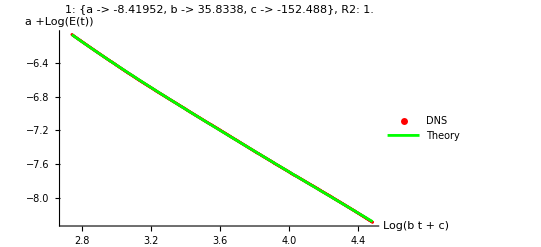

```mathematica
FitETData[1]
```

InterpolatingFunction::dmval: Input value {-14.6081} lies outside the range of data in the interpolating function. Extrapolation will be used.

NonlinearModelFit::nrnum: The function value Divide[355.987 + <<799>> + Power[<<2>>], 2] is not a real number at {a,b,c} = {-10.223,-4.1846,100.879}.

InterpolatingFunction::dmval: Input value {-14.6081} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Divide[355.987 + <<799>> + Power[<<2>>], 2] is not a real number at {a,b,c} = {-10.223,-4.1846,100.879}.

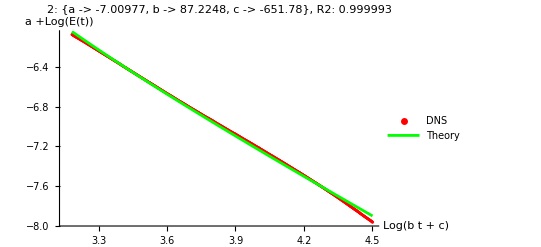

```mathematica
FitETData[2]
```

InterpolatingFunction::dmval: Input value {-5.44637} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value 1/2 (3.86797×10^11+(«1»)^2) is not a real number at {a,b,c} = {-22001.1,1.27748,-53.8064}.

NonlinearModelFit::nrnum: The function value 1/2 (3.86797×10^11+(-21995.+«1»[-18.4362+3.14159 ⅈ])^2) is not a real number at {a,b,c} = {-22001.1,1.27748,-53.8064}.

NonlinearModelFit::nrnum: The function value 1/2 (3.86797×10^11+(-21995.+«1»[-19.9267+3.14159 ⅈ])^2) is not a real number at {a,b,c} = {-22001.1,1.27748,-53.8064}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::steperr: Error in step computation.

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

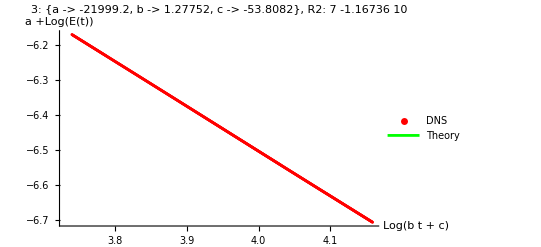

```mathematica
FitETData[3]
```

```mathematica
FitETData[4]
```

InterpolatingFunction::dmval: Input value {-5.22547} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

NonlinearModelFit::nrnum: The function value 1/2 (639.383+(«1»)^2) is not a real number at {a,t0} = {-13.6792,-30.2138}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

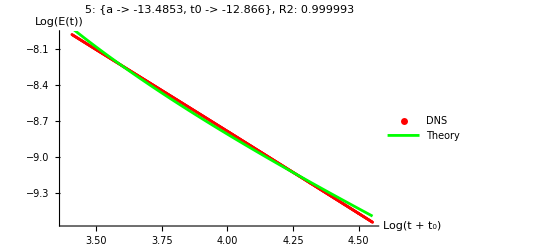

```mathematica
FitETData[5]
```

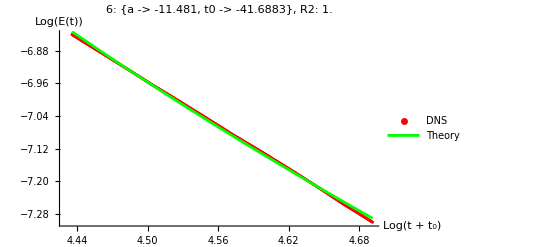

```mathematica
FitETData[6]
```

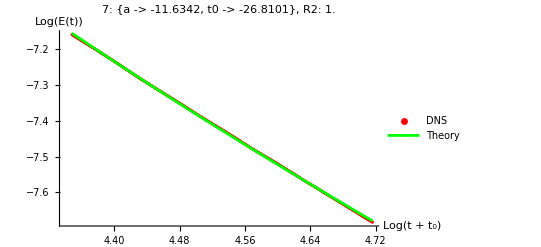

```mathematica
FitETData[7]
```

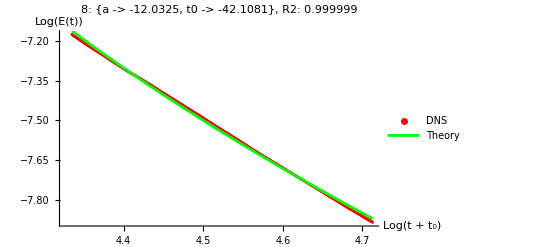

```mathematica
FitETData[8]
```

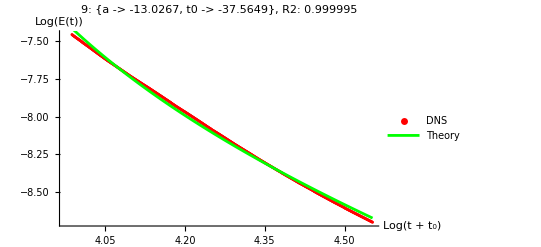

```mathematica
FitETData[9]
```

InterpolatingFunction::dmval: Input value {-17.24} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value 1/2 (460.881+(«1»)^2) is not a real number at {a,t0} = {-14.1022,-7.5658}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

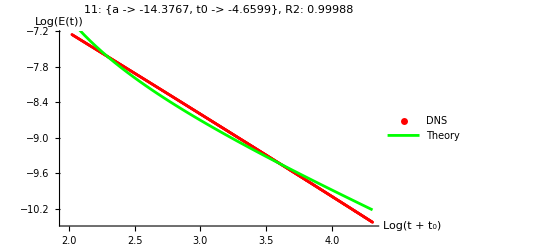

```mathematica
FitETData[11]
```

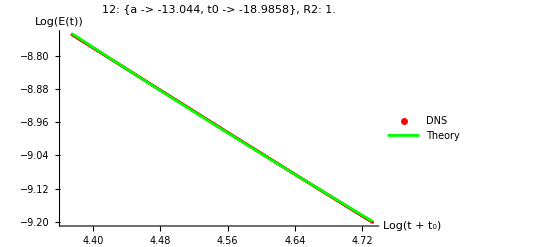

```mathematica
FitETData[12]
```

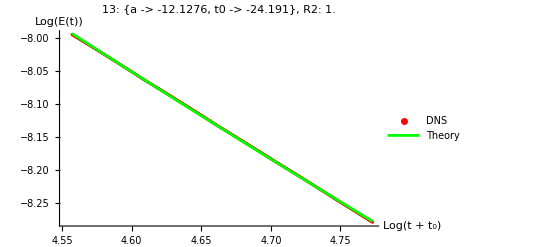

```mathematica
FitETData[13]
```

InterpolatingFunction::dmval: Input value {-17.0464} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.62681} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.93367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value 1/2 (6985.78+(«1»)^2) is not a real number at {a,t0} = {-10.0865,-26.2566}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

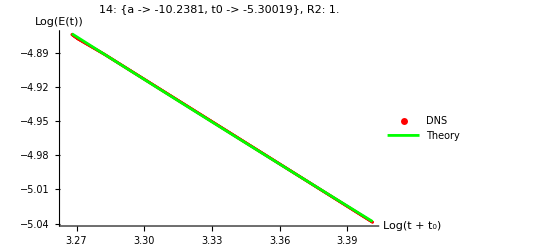

```mathematica
FitETData[14]
```

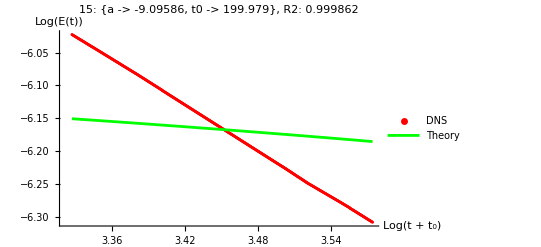

```mathematica
FitETData[15]
```

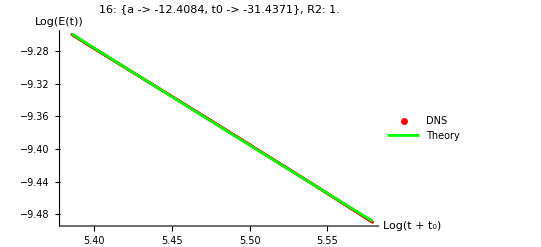

```mathematica
FitETData[16]
```